{{310,0.638961},{275,0.563911},{223,0.452408},{179,0.35806},{147,0.289443},{121,0.233691}}

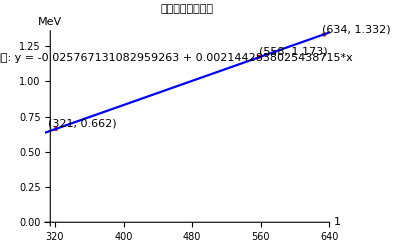

拟合方程: -0.0257671+0.00214428 x

拟合参数： | Estimate | Standard Error | t-Statistic | P-Value
1 | -0.0257671 | 0.00651454 | -3.95532 | 0.157649
x | 0.00214428 | 0.0000124883 | 171.703 | 0.00370763

决定系数R.b2：0.999966

标准误差：8.31327×10^-6

```mathematica
(*定义数据点*)
data={{321,0.662},{558,1.173},{634,1.332}};

(*线性回归拟合*)
fit=LinearModelFit[data,x,x];

(*新的数据点*)
newData={310,275,223,179,147,121};

(*计算能量*)
calculatedEnergies=fit[#]&/@newData;

(*输出新数据点及其对应的能量*)
newDataWithEnergies=Transpose[{newData,calculatedEnergies}]

(*获取拟合方程*)
fitFunction=fit["BestFit"];

(*绘制数据点和拟合直线，并标出数据点的数值和拟合方程*)
Show[ListPlot[data,PlotStyle->{Red,PointSize[Large]},AxesLabel->{"1","MeV"}],Plot[fitFunction,{x,300,650},PlotStyle->Blue],PlotLabel->"数据点及拟合直线",Epilog->{Text["("<>ToString[data[[1,1]]]<>", "<>ToString[data[[1,2]]]<>")",{312,0.662},{-1,-1}],Text["("<>ToString[data[[2,1]]]<>", "<>ToString[data[[2,2]]]<>")",{558,1.173},{-1,-1}],Text["("<>ToString[data[[3,1]]]<>", "<>ToString[data[[3,2]]]<>")",{631,1.332},{-1,-1}],Text["拟合直线: y = "<>ToString[Normal[fitFunction],InputForm],{450,1.2},{0,1}]}]

(*计算误差分析*)
Print["拟合方程: ",fitFunction];
Print["拟合参数：",fit["ParameterTable"]];
Print["决定系数R.b2：",fit["RSquared"]];
Print["标准误差：",fit["EstimatedVariance"]];
```

```mathematica
N[2325377/5965611,15]
```

0.3897969545785

```mathematica
(N[2325377/5965611,15]-0.39)/0.39
```

-0.000520629